# Fourier discrete cosine transform

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

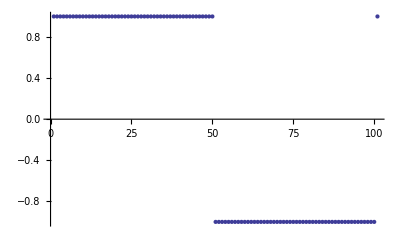

```mathematica
data=Table[SquareWave[{-1,1},x],{x,0,1,0.01}];
n=Length[data];
ListPlot[data]
```

finds the Fourier discrete cosine transform of type 3.

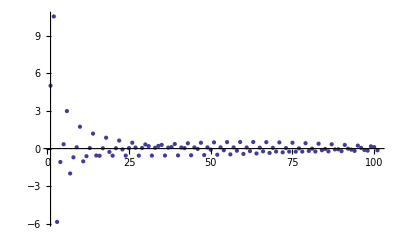

```mathematica
dct=FourierDCT[data,3];
ListPlot[dct,PlotRange->All]
```

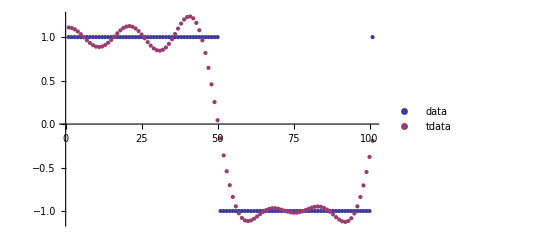

```mathematica
tdata=FourierDCT[PadRight[Take[dct,10],n]];
ListPlot[{data,tdata},PlotLegends->{"data","tdata"}]
```

```mathematica
tdata=FourierDCT[FourierDCT[data,3]];
```

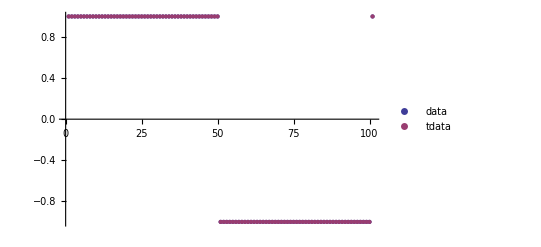

```mathematica
ListPlot[{data,tdata},PlotLegends->{"data","tdata"}]
```